```mathematica
(*This first part is what you already know*)
```

```mathematica
Clear[kt,u, d,g,rs, a, b,x, rho1,rho2,rho3, rhodash, rhodash1, rhodash2,rhodash3, lgs, lgs1,lgs2, lgs3,lgs4,lgs5,lgs6,k,fk,kulim0,kliminf,dk]
```

```mathematica
kt = 1;
rs = 1;
```

```mathematica
(*Transition matrix for Barrier*)
```

```mathematica
w = {{-g,g},{g,-g}};
```

```mathematica
(*evec = Eigenvectors[w] Use hard coded definition instead to assure correct order of eigenvalues *)
```

```mathematica
evec = {{1,1},{-1,1}}
```

{{1,1},{-1,1}}

```mathematica
s = Transpose[{Normalize[evec[[1]]],Normalize[evec[[2]]]}]
```

{{1/(√2),-1/(√2)},{1/(√2),1/(√2)}}

```mathematica
invs = Simplify[Assuming[{ab>0, ba>0},Inverse[s]]]
```

{{1/(√2),1/(√2)},{-1/(√2),1/(√2)}}

```mathematica
diagw = Simplify[invs.w.s]
```

{{0,0},{0,-2 g}}

```mathematica
(*Assembly of matching matrix*)
```

```mathematica
bcu = {{1,0},{0,Exp[u/kt]}}
```

{{1,0},{0,ⅇ^u}}

```mathematica
(*Do handy substitutions first before things get out of hand!*)
```

```mathematica
rhodash[r_] = {{1, 1/r, 0, 0},{0, 0, Exp[-Sqrt[Abs[diagw[[2,2]]]/d]r]/r,Exp[Sqrt[Abs[diagw[[2,2]]]/d]r]/r}} /.√2 √(1/d) √Abs[g]->x
```

{{1,1/r,0,0},{0,0,ⅇ^(-r x)/r,ⅇ^(r x)/r}}

```mathematica
lgs1 = Join[rhodash[rs],{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},2];
lgs2 = Join[rhodash[a], -invs.bcu.s.rhodash[a], {{0,0,0,0},{0,0,0,0}},2];
lgs3 = Join[rhodash'[a],-rhodash'[a],{{0,0,0,0},{0,0,0,0}},2];
lgs4= Join[{{0,0,0,0},{0,0,0,0}},invs.bcu.s.rhodash[b],-rhodash[b],2];
lgs5 = Join[{{0,0,0,0},{0,0,0,0}},rhodash'[b],-rhodash'[b],2];
lgs6 = Join[{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{1,0,0,0},{0,0,0,Infinity}},2];
```

```mathematica
lgs = Join[lgs1, lgs2, lgs3, lgs4,lgs5,lgs6,1];
```

```mathematica
lgs = lgs[[1;;11,1;;11]];
```

```mathematica
(*Calculation of matching constants*)
```

```mathematica
c =Assuming[{g>0,d>0,kt>0,b>a>rs>0}, LinearSolve[lgs,Transpose[{{0,0,0,0,0,0,0,0,0,0,1}}]]];
```

```mathematica
c = Assuming[b > a > rs > 0,Simplify[c]];
```

```mathematica
c = Join[c,{{0}}];
```

```mathematica
(*Check, if matching worked out*)
```

```mathematica
Simplify[lgs.c[[1;;11]]]
```

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{1}}

```mathematica
rhodash1[r_] = rhodash[r].c[[1;;4]];
```

```mathematica
Simplify[rhodash1[rs]]
```

{{0},{0}}

```mathematica
rhodash2[r_] = rhodash[r].c[[5;;8]];
```

```mathematica
rhodash3[r_] = rhodash[r].c[[9;;12]];
```

```mathematica
Simplify[invs.bcu.s.rhodash2[b] - rhodash3[b]]
Simplify[rhodash2'[b] - rhodash3'[b]]
Simplify[rhodash3[Infinity]]
```

{{0},{0}}

{{0},{0}}

{{1},{0 ⅇ^(x (-∞))}}

```mathematica
(*Calculatio normalization of density profiles*)
```

```mathematica
n = Limit[Total[Total[s.rhodash3[r]]],r->Infinity]
```

√2

```mathematica
(*Calculate density profiles*)
```

```mathematica
rho1[r_] = s.rhodash1[r]/n;
rho2[r_] = s.rhodash2[r]/n;
rho3[r_] = s.rhodash3[r]/n;
```

```mathematica
rhom1[r_] =Part[rho1[r],1]+ Part[rho1[r],2];
rhom2[r_] =Part[rho2[r],1]+ Part[rho2[r],2];
rhom3[r_] =Part[rho3[r],1]+ Part[rho3[r],2];
```

```mathematica
(*Calculate absorption rate (omit the 4 pi D Rs)*)
```

```mathematica
rho1dash[r_] := rhom1'[r]
```

```mathematica
k:=  Simplify[Total[rho1dash[1]]]
```

```mathematica
(*Make absorption rate a function of its parameters*)
```

```mathematica
fk[a_,b_,u_,x_]:=(-2 ⅇ^(u+2 (1+b) x) (1+a x) (-1+b x)-2 b ⅇ^((2+a+b) x) x (1+b x)+2 b ⅇ^((3 a+b) x) x (1+b x)-4 b ⅇ^(u+3 a x+b x) x (1+b x)+2 b ⅇ^(2 u+3 a x+b x) x (1+b x)+4 b ⅇ^(u+(2+a+b) x) x (1+b x)-2 b ⅇ^(2 u+(2+a+b) x) x (1+b x)+ⅇ^(4 a x) (-1+a x) (1+b x)-ⅇ^(2 (1+a) x) (-1+a x) (1+b x)-2 ⅇ^(u+4 a x) (-1+a x) (1+b x)+ⅇ^(2 u+4 a x) (-1+a x) (1+b x)-2 ⅇ^(u+2 (1+a) x) (1+a x) (1+b x)-ⅇ^(2 (u+x+b x)) (1+a x) (1+b x)-ⅇ^(2 (u+(a+b) x)) (-1+3 a x) (1+b x)+ⅇ^(2 (u+x+a x)) (1+3 a x) (1+b x)+ⅇ^(2 (1+b) x) (1+a x) (-1+3 b x)-ⅇ^(2 (a+b) x) (1+a x) (-1+3 b x)+2 ⅇ^(u+2 (a+b) x) (-1+b x+a (x-5 b x^2)))/(2 ⅇ^(u+2 (1+b) x) (1+a x) (1+(-2+b) x)+2 ⅇ^((2+a+b) x) x (-2+a-a x+a^2 x-b x)-4 ⅇ^(u+(2+a+b) x) x (-2+a-a x+a^2 x-b x)+2 ⅇ^(2 u+(2+a+b) x) x (-2+a-a x+a^2 x-b x)+2 ⅇ^(u+2 (1+a) x) (-1+(-2+a) x) (1+b x)+ⅇ^(4 a x) (-1+a x) (1+b x)-2 ⅇ^(u+4 a x) (-1+a x) (1+b x)+ⅇ^(2 u+4 a x) (-1+a x) (1+b x)+ⅇ^(2 (u+x+a x)) (1+(2+a) x) (1+b x)-ⅇ^(2 (1+a) x) (-1+(-2+3 a) x) (1+b x)+ⅇ^(2 (1+b) x) (1+a x) (-1+(2+b) x)-ⅇ^(2 (u+x+b x)) (1+a x) (1+(-2+3 b) x)-ⅇ^(2 (u+(a+b) x)) (-1+(4+a-3 b) x+3 (a (-2+b)+2 b) x^2)-ⅇ^(2 (a+b) x) (-1+(4-3 a+b) x+(-2 b+a (2+3 b)) x^2)-2 ⅇ^(u+2 (a+b) x) (1+(-4+a+b) x+(-2 b+a (2+5 b)) x^2)+2 ⅇ^((3 a+b) x) x (2+a^2 x+b x-a (1+x))-4 ⅇ^(u+3 a x+b x) x (2+a^2 x+b x-a (1+x))+2 ⅇ^(2 u+3 a x+b x) x (2+a^2 x+b x-a (1+x)))
```

```mathematica
dk = Simplify[D[k,x]];
```

```mathematica
(*Calculate limiting behaviour for x ->0*)
```

```mathematica
Assuming[b > a > 1,Limit[k,x->0]]
```

(b-b ⅇ^u+a (-1-2 b+ⅇ^u))/(2 (b-b ⅇ^u+a (-1-b+ⅇ^u)))

```mathematica
(b-b ⅇ^u+a (-1-2 b+ⅇ^u))/(2 (b-b ⅇ^u+a (-1-b+ⅇ^u)))
```

(b-b ⅇ^u+a (-1-2 b+ⅇ^u))/(2 (b-b ⅇ^u+a (-1-b+ⅇ^u)))

```mathematica
klim0[a_,b_,u_]:=(b-b ⅇ^u+a (-1-2 b+ⅇ^u))/(2(b-b ⅇ^u+a (-1-b+ⅇ^u)))
```

```mathematica
(*Calculate limiting behaviour for x -> oo by hand, since mathematica resists do it..*)
```

```mathematica
Simplify[(-ⅇ^(2 (u+(a+b) x)) (-1+3 a x) (1+b x)-ⅇ^(2 (a+b) x) (1+a x) (-1+3 b x)+2 ⅇ^(u+2 (a+b) x) (-1+b x+a (x-5 b x^2)))/(-ⅇ^(2 (u+(a+b) x)) (-1+(4+a-3 b) x+3 (a (-2+b)+2 b) x^2)-ⅇ^(2 (a+b) x) (-1+(4-3 a+b) x+(-2 b+a (2+3 b)) x^2)-2 ⅇ^(u+2 (a+b) x) (1+(-4+a+b) x+(-2 b+a (2+5 b)) x^2))]
```

((1+a x+ⅇ^u (-1+3 a x)) (-1+3 b x+ⅇ^u (1+b x)))/(-1+(4-3 a+b) x+(2 a-2 b+3 a b) x^2+ⅇ^(2 u) (-1+(4+a-3 b) x+3 (a (-2+b)+2 b) x^2)+2 ⅇ^u (1+(-4+a+b) x+(2 a-2 b+5 a b) x^2))

```mathematica
Limit[((1+a x+ⅇ^u (-1+3 a x)) (-1+3 b x+ⅇ^u (1+b x)))/(-1+(4-3 a+b) x+(2 a-2 b+3 a b) x^2+ⅇ^(2 u) (-1+(4+a-3 b) x+3 (a (-2+b)+2 b) x^2)+2 ⅇ^u (1+(-4+a+b) x+(2 a-2 b+5 a b) x^2)),x->Infinity]
```

(a b (3+ⅇ^u))/(2 b (-1+ⅇ^u)+a (2-2 ⅇ^u+b (3+ⅇ^u)))

```mathematica
kliminf[a_,b_,u_]:=(a b (3+ⅇ^u))/(2 b (-1+ⅇ^u)+a (2-2 ⅇ^u+b (3+ⅇ^u)))
```

```mathematica
(*Do some plot of the results*)
```

4

8

-4

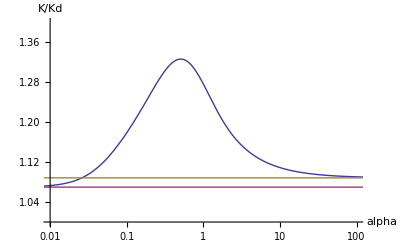

```mathematica
a = 4
b = 8
u = -4
LogLinearPlot[{fk[a,b,u,x],klim0[a,b,u],kliminf[a,b,u]}, {x,0.001,1000},PlotRange->{{0.01,100},{1,1.4}},AxesLabel->{alpha, K/Kd}]
Clear[a,b,u,x]
```

```mathematica
4
```

4

```mathematica
(*Limiting behaviour is somewhat different from what we expected and not very intuitive to understand at first glance... BUT this looks a lot better than everything i've had so far.*)
```

```mathematica
(*Now lets have a look at the approximate behaviour of k for x->oo and x->0.*)
```

```mathematica
(*Therefore for x->oo collect the terms with largest exponent from numerator and denominator of k*)
```

```mathematica
klargex =Simplify[((1+a x+ⅇ^u (-1+3 a x)) (-1+3 b x+ⅇ^u (1+b x)))/(-1+(4-3 a+b) x+(2 a-2 b+3 a b) x^2+ⅇ^(2 u) (-1+(4+a-3 b) x+3 (a (-2+b)+2 b) x^2)+2 ⅇ^u (1+(-4+a+b) x+(2 a-2 b+5 a b) x^2))]
```

((1+a x+ⅇ^u (-1+3 a x)) (-1+3 b x+ⅇ^u (1+b x)))/(-1+(4-3 a+b) x+(2 a-2 b+3 a b) x^2+ⅇ^(2 u) (-1+(4+a-3 b) x+3 (a (-2+b)+2 b) x^2)+2 ⅇ^u (1+(-4+a+b) x+(2 a-2 b+5 a b) x^2))

```mathematica
Collect[((1+a x+ⅇ^u (-1+3 a x)) (-1+3 b x+ⅇ^u (1+b x))),x]
```

-1+2 ⅇ^u-ⅇ^(2 u)+(-a+3 b-2 a ⅇ^u-2 b ⅇ^u+3 a ⅇ^(2 u)-b ⅇ^(2 u)) x+(3 a b+10 a b ⅇ^u+3 a b ⅇ^(2 u)) x^2

```mathematica
Collect[(-1+(4-3 a+b) x+(2 a-2 b+3 a b) x^2+ⅇ^(2 u) (-1+(4+a-3 b) x+3 (a (-2+b)+2 b) x^2)+2 ⅇ^u (1+(-4+a+b) x+(2 a-2 b+5 a b) x^2)),x]
```

-1+2 ⅇ^u-ⅇ^(2 u)+(4-3 a+b+2 (-4+a+b) ⅇ^u+(4+a-3 b) ⅇ^(2 u)) x+(2 a-2 b+3 a b+2 (2 a-2 b+5 a b) ⅇ^u+3 (a (-2+b)+2 b) ⅇ^(2 u)) x^2

```mathematica
(*Then, from each collect the leading terms in x and simplify*)
```

```mathematica
fklargex[a_,b_,u_,x_] :=Simplify[((-a+3 b-2 a ⅇ^u-2 b ⅇ^u+3 a ⅇ^(2 u)-b ⅇ^(2 u)) x+(3 a b+10 a b ⅇ^u+3 a b ⅇ^(2 u)) x^2)/((4-3 a+b+2 (-4+a+b) ⅇ^u+(4+a-3 b) ⅇ^(2 u)) x+(2 a-2 b+3 a b+2 (2 a-2 b+5 a b) ⅇ^u+3 (a (-2+b)+2 b) ⅇ^(2 u)) x^2)]
```

```mathematica
Simplify[((-a+3 b-2 a ⅇ^u-2 b ⅇ^u+3 a ⅇ^(2 u)-b ⅇ^(2 u)) x+(3 a b+10 a b ⅇ^u+3 a b ⅇ^(2 u)) x^2)/((4-3 a+b+2 (-4+a+b) ⅇ^u+(4+a-3 b) ⅇ^(2 u)) x+(2 a-2 b+3 a b+2 (2 a-2 b+5 a b) ⅇ^u+3 (a (-2+b)+2 b) ⅇ^(2 u)) x^2)]
```

(-b (-3+2 ⅇ^u+ⅇ^(2 u))+a (1+3 ⅇ^u) (-1+3 b x+ⅇ^u (1+b x)))/((-1+ⅇ^u) (4 (-1+ⅇ^u)+b (1+3 ⅇ^u) (-1+2 x))+a (-3+2 x+3 b x+ⅇ^(2 u) (1+3 (-2+b) x)+2 ⅇ^u (1+(2+5 b) x)))

```mathematica
(*For x->0 do taylor expansion*)
```

```mathematica
ksmallx =Simplify[Series[k,{x,0,2}]]
```

(b-b ⅇ^u+a (-1-2 b+ⅇ^u))/(2 (b-b ⅇ^u+a (-1-b+ⅇ^u)))+((a-b)^2 (-1+ⅇ^u)^2 x)/(4 (a (1+b-ⅇ^u)+b (-1+ⅇ^u))^2)+1/(24 (b-b ⅇ^u+a (-1-b+ⅇ^u))^3)(a-b)^2 ⅇ^-u (-1+ⅇ^u)^2 (-2 a^4 b (1+b-ⅇ^u)-a^3 b (-5+b^2+6 ⅇ^u-ⅇ^(2 u)+2 b (-3+ⅇ^u))+b (-1+ⅇ^u) (-ⅇ^u+3 b^2 (-1+ⅇ^u))-a^2 b (-4 b (-1+ⅇ^u)+3 (-1+ⅇ^u)^2+b^2 (-5+2 ⅇ^u))-a (4 b ⅇ^u-ⅇ^u (-1+ⅇ^u)+b^3 (7-8 ⅇ^u+ⅇ^(2 u)))) x^2+O[x]^3

```mathematica
fksmallx[a_,b_,u_,x_] :=(b-b ⅇ^u+a (-1-2 b+ⅇ^u))/(2 (b-b ⅇ^u+a (-1-b+ⅇ^u)))+((a-b)^2 (-1+ⅇ^u)^2 x)/(4 (a (1+b-ⅇ^u)+b (-1+ⅇ^u))^2)+1/(24 (b-b ⅇ^u+a (-1-b+ⅇ^u))^3)(a-b)^2 ⅇ^-u (-1+ⅇ^u)^2 (-2 a^4 b (1+b-ⅇ^u)-a^3 b (-5+b^2+6 ⅇ^u-ⅇ^(2 u)+2 b (-3+ⅇ^u))+b (-1+ⅇ^u) (-ⅇ^u+3 b^2 (-1+ⅇ^u))-a^2 b (-4 b (-1+ⅇ^u)+3 (-1+ⅇ^u)^2+b^2 (-5+2 ⅇ^u))-a (4 b ⅇ^u-ⅇ^u (-1+ⅇ^u)+b^3 (7-8 ⅇ^u+ⅇ^(2 u)))) x^2
```

```mathematica
(* See some examplary plots for the results*)
```

4

6

4

0.3

0.2

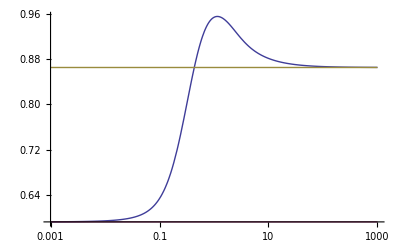

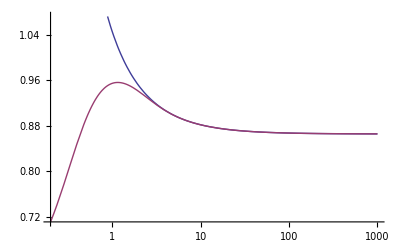

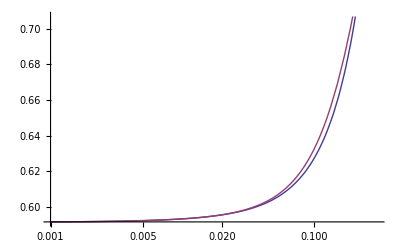

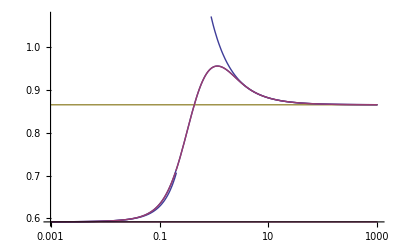

```mathematica
a = 4
b = 6
u = 4
pmax =0.3
pmin =0.2
p1 =LogLinearPlot[{fk[a,b,u,x],klim0[a,b,u],kliminf[a,b,u]}, {x,0.001,1000}]
p2 =LogLinearPlot[{fklargex[a,b,u,x],fk[a,b,u,x]}, {x,pmin,1000}]
p3 =LogLinearPlot[{fksmallx[a,b,u,x],fk[a,b,u,x]}, {x,0.001,pmax}]
Show[p1,p2,p3,PlotRange -> All]
Clear[a,b,u,x]
```

```mathematica
klimu = Simplify[Limit[Collect[Numerator[k],ⅇ^u]/Collect[Denominator[k],ⅇ^u],u->Infinity]]
```

-((1+b x) (2 b ⅇ^((2+a+b) x) x-2 b ⅇ^((3 a+b) x) x+ⅇ^(4 a x) (1-a x)+ⅇ^(2 (1+b) x) (1+a x)+ⅇ^(2 (a+b) x) (-1+3 a x)-ⅇ^(2 (1+a) x) (1+3 a x)))/(2 ⅇ^((2+a+b) x) x (-2+a-a x+a^2 x-b x)+ⅇ^(4 a x) (-1+a x) (1+b x)+ⅇ^(2 (1+a) x) (1+(2+a) x) (1+b x)-ⅇ^(2 (1+b) x) (1+a x) (1+(-2+3 b) x)-ⅇ^(2 (a+b) x) (-1+(4+a-3 b) x+3 (a (-2+b)+2 b) x^2)+2 ⅇ^((3 a+b) x) x (2+a^2 x+b x-a (1+x)))

```mathematica
fklimu[a_,b_,x_]:=-((1+b x) (2 b ⅇ^((2+a+b) x) x-2 b ⅇ^((3 a+b) x) x+ⅇ^(4 a x) (1-a x)+ⅇ^(2 (1+b) x) (1+a x)+ⅇ^(2 (a+b) x) (-1+3 a x)-ⅇ^(2 (1+a) x) (1+3 a x)))/(2 ⅇ^((2+a+b) x) x (-2+a-a x+a^2 x-b x)+ⅇ^(4 a x) (-1+a x) (1+b x)+ⅇ^(2 (1+a) x) (1+(2+a) x) (1+b x)-ⅇ^(2 (1+b) x) (1+a x) (1+(-2+3 b) x)-ⅇ^(2 (a+b) x) (-1+(4+a-3 b) x+3 (a (-2+b)+2 b) x^2)+2 ⅇ^((3 a+b) x) x (2+a^2 x+b x-a (1+x)))
```

4

6

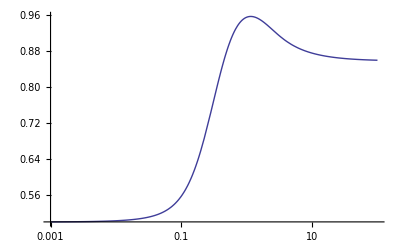

```mathematica
a = 4
b = 6
p1 =LogLinearPlot[{fklimu[a,b,x]}, {x,0.001,100}]
Clear[a,b]
```

2

FindMaximum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {1.78809×10^-11, 0.0000591872, 1.80615×10^-11}, is returned.

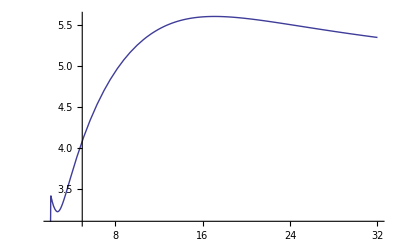

```mathematica
(*Intuitive guess: if the diffusion time of particles across the barrier is equal to the inverse of the switching rate, resonance accures. If so, the following plot would be (more or less) constant.. Well, obviously not.*)
a=2
Plot[(x/.Last[FindMaximum[{fklimu[a,b,x],x>0},{x,1}]])*(b-a),{b,a+0.1,a+30}]
```

```mathematica
x/.Last[FindMaximum[{fklimu[3,4,x],x>0},{x,1}]]
```

2.62942

```mathematica
tmp[z] := klargex/.x->1/z
```

```mathematica
Series[tmp[z], {z,0,2}]
```

(b (3+ⅇ^u))/(2 (1+b-ⅇ^u+b ⅇ^u))+((-1+ⅇ^u)^2 (-4+8 b+3 b^2-12 ⅇ^u+8 b ⅇ^u+b^2 ⅇ^u) z)/(8 (1+3 ⅇ^u) (1+b-ⅇ^u+b ⅇ^u)^2)+((-2+b) (-1+ⅇ^u)^3 (-8+4 b+3 b^2-8 ⅇ^u+4 b ⅇ^u+b^2 ⅇ^u) z^2)/(32 (1+3 ⅇ^u) (1+b-ⅇ^u+b ⅇ^u)^3)+O[z]^3

```mathematica
Series[klargex, {x,Infinity,2}]
```

(b (3+ⅇ^u))/(2 (1+b-ⅇ^u+b ⅇ^u))+((-1+ⅇ^u)^2 (-4+8 b+3 b^2-12 ⅇ^u+8 b ⅇ^u+b^2 ⅇ^u))/(8 (1+3 ⅇ^u) (1+b-ⅇ^u+b ⅇ^u)^2 x)+((-2+b) (-1+ⅇ^u)^3 (-8+4 b+3 b^2-8 ⅇ^u+4 b ⅇ^u+b^2 ⅇ^u))/(32 (1+3 ⅇ^u) (1+b-ⅇ^u+b ⅇ^u)^3 x^2)+O[1/x]^3

```mathematica
klxnumerator[a_,t_,u_] := (-a^2-2 a b+3 a^2 b-3 b^2+3 a b^2-3 a^2 ⅇ^u+2 a b ⅇ^u+a^2 b ⅇ^u-b^2 ⅇ^u+a b^2 ⅇ^u)/.b->a+t
```

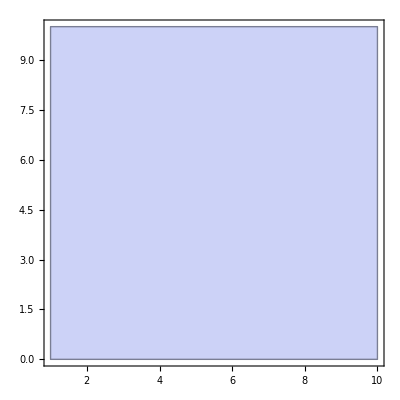

```mathematica
RegionPlot[klxnumerator[a,t,-100]>0, {a,1,10}, {t,0,10}]
```

```mathematica
Assuming[{b>a>0,Element[u,Reals]},Simplify[2 (-1+ⅇ^u)^2 (-a^2-2 a b+3 a^2 b-3 b^2+3 a b^2-3 a^2 ⅇ^u+2 a b ⅇ^u+a^2 b ⅇ^u-b^2 ⅇ^u+a b^2 ⅇ^u)>0]]
```

(-1+ⅇ^u)^2>0

```mathematica
Assuming[b>a>0,Simplify[(-b^2 (3+ⅇ^u)+a^2 (-1-3 ⅇ^u+b (3+ⅇ^u))+a b (2 (-1+ⅇ^u)+b (3+ⅇ^u)))>0]]
```

b (8 (1+ⅇ^u)+b (3+ⅇ^u))>4+12 ⅇ^u

```mathematica
Solve[a (a (-1-3 ⅇ^u+b (3+ⅇ^u))+b (2 (-1+ⅇ^u)+b (3+ⅇ^u)))==b^2 (3+ⅇ^u),{a,b,u}]
```

Solve::ivar: 2 is not a valid variable.

Solve[2 (2 (-1-3 ⅇ^u+b (3+ⅇ^u))+b (2 (-1+ⅇ^u)+b (3+ⅇ^u)))==b^2 (3+ⅇ^u),{2,b,u}]

```mathematica
Assuming[{b>a>0,Element[u,Reals]},Simplify[a (a (-1-3 ⅇ^u+b (3+ⅇ^u))+b (2 (-1+ⅇ^u)))>0]]
```

True

```mathematica
b (a (3+ⅇ^u))>a+3 a ⅇ^u
```

2 b (3+ⅇ^u)>2+6 ⅇ^u

```mathematica
Assuming[{b>a>0,Element[u,Reals]},Simplify[b (a (3+ⅇ^u))>a+3 a ⅇ^u]]
```

b (3+ⅇ^u)>1+3 ⅇ^u

```mathematica
Assuming[{b>a>0,Element[u,Reals]},Solve[b (3+ⅇ^u)>1+3 ⅇ^u]]
```

Solve::fdimc: When parameter values satisfy the condition (ⅇ^u > -3 && b > 1 + 3\ ⅇ^u/3 + ⅇ^u) || (ⅇ^u < -3 && b < 1 + 3\ ⅇ^u/3 + ⅇ^u), the solution set contains a full-dimensional component; use Reduce for complete solution information.

{}

```mathematica
RegionPlot3D[(-b^2 (3+ⅇ^u)+a^2 (-1-3 ⅇ^u+b (3+ⅇ^u))+a b (2 (-1+ⅇ^u)+b (3+ⅇ^u)))<0&&a<b,{b,2,100},{u,-50,50},{a,1,100},AxesLabel->Automatic]
```

-Graphics3D-

-Graphics3D-